Integrate::ilim: Invalid integration variable or limit(s) in {-0.999959,-1,0}.

Integrate::ilim: Invalid integration variable or limit(s) in {-0.999959,0,1}.

Integrate::ilim: Invalid integration variable or limit(s) in {-0.999959,-1,0}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

NIntegrate::itraw: Raw object -0.999959 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

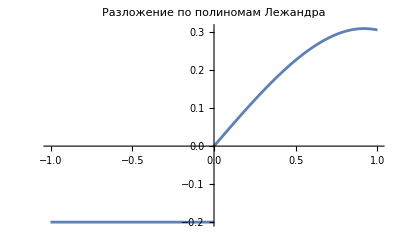

Integrate::ilim: Invalid integration variable or limit(s) in {-0.999959,-1,0}.

Integrate::ilim: Invalid integration variable or limit(s) in {-0.999959,0,1}.

Integrate::ilim: Invalid integration variable or limit(s) in {-0.999959,-1,0}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

NIntegrate::itraw: Raw object -0.999959 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

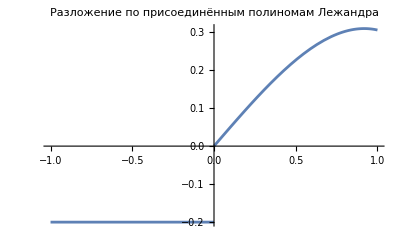

Integrate::ilim: Invalid integration variable or limit(s) in {-0.999959,-1,0}.

Integrate::ilim: Invalid integration variable or limit(s) in {-0.999959,0,1}.

Integrate::ilim: Invalid integration variable or limit(s) in {-0.999959,-1,0}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

NIntegrate::itraw: Raw object -0.999959 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

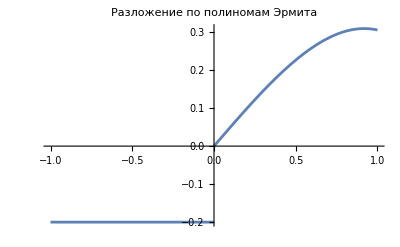

```mathematica
(*Определение функции с доопределением в точке x=0*)f[x_]:=Piecewise[{{-1/5,-1<x<0},{-1/10,x==0},{BesselI[1,x] Cos[x],0<x<1}}]

(*А.Разложение по полиномам Лежандра*)
nMax=5; (*Максимальное количество частичных сумм*)

(*Вычисление коэффициентов a_n*)
a[n_]:=(2 n+1)/2*(Integrate[LegendreP[n,x]*-1/5,{x,-1,0}]+Integrate[LegendreP[n,x]*BesselI[1,x] Cos[x],{x,0,1}])

(*Частичные суммы S_n(x)*)
S[n_,x_]:=Sum[a[k] LegendreP[k,x],{k,0,n}]

(*Построение графиков для полиномов Лежандра*)
Plot[{f[x],Table[S[n,x],{n,1,nMax}]},{x,-1,1},PlotLegends->Append[{"f(x)"},Table["S"<>ToString[n]<>"(x)",{n,1,nMax}]],PlotLabel->"Разложение по полиномам Лежандра"]

(*Б.Разложение по присоединённым полиномам Лежандра второго порядка*)

(*Вычисление коэффициентов b_n*)
b[n_]:=(2 n+1)/2*(Integrate[LegendreP[n,2,x]*-1/5,{x,-1,0}]+Integrate[LegendreP[n,2,x]*BesselI[1,x] Cos[x],{x,0,1}])

(*Частичные суммы T_n(x)*)
T[n_,x_]:=Sum[b[k] LegendreP[k,2,x],{k,0,n}]

(*Построение графиков для присоединённых полиномов Лежандра*)
Plot[{f[x],Table[T[n,x],{n,1,nMax}]},{x,-1,1},PlotLegends->Append[{"f(x)"},Table["T"<>ToString[n]<>"(x)",{n,1,nMax}]],PlotLabel->"Разложение по присоединённым полиномам Лежандра"]

(*В.Разложение по полиномам Эрмита*)

(*Вычисление коэффициентов c_n*)
c[n_]:=1/(Sqrt[Pi] 2^n n!)*(Integrate[HermiteH[n,x]*-1/5*Exp[-x^2],{x,-1,0}]+Integrate[HermiteH[n,x]*BesselI[1,x] Cos[x]*Exp[-x^2],{x,0,1}])

(*Частичные суммы U_n(x)*)
U[n_,x_]:=Sum[c[k] HermiteH[k,x],{k,0,n}]

(*Построение графиков для полиномов Эрмита*)
Plot[{f[x],Table[U[n,x],{n,1,nMax}]},{x,-1,1},PlotLegends->Append[{"f(x)"},Table["U"<>ToString[n]<>"(x)",{n,1,nMax}]],PlotLabel->"Разложение по полиномам Эрмита"]

(*Нахождение оптимального n для каждого разложения*)

(*Для полиномов Лежандра*)
errorLegendre[n_]:=NMaxValue[{Abs[f[x]-S[n,x]],-1<x<1},x,WorkingPrecision->20]
optimalNLegendre=First@Select[Range[1,10],errorLegendre[#]<=0.1 (MaxValue[f[x],{x,-1,1}]-MinValue[f[x],{x,-1,1}])&]

(*Для присоединённых полиномов Лежандра*)
errorAssociatedLegendre[n_]:=NMaxValue[{Abs[f[x]-T[n,x]],-1<x<1},x,WorkingPrecision->20]
optimalNAssociatedLegendre=First@Select[Range[1,10],errorAssociatedLegendre[#]<=0.1 (MaxValue[f[x],{x,-1,1}]-MinValue[f[x],{x,-1,1}])&]

(*Для полиномов Эрмита*)
errorHermite[n_]:=NMaxValue[{Abs[f[x]-U[n,x]],-1<x<1},x,WorkingPrecision->20]
optimalNHermite=First@Select[Range[1,10],errorHermite[#]<=0.1 (MaxValue[f[x],{x,-1,1}]-MinValue[f[x],{x,-1,1}])&]

(*Вывод оптимальных n*)
{optimalNLegendre,optimalNAssociatedLegendre,optimalNHermite}
```